```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/s1220054/Dissertation/Dissertation/DiSamp/src

```mathematica
chidata =Import["chi.txt", "CSV"]
```

{{1,284},{2,864},{3,1201},{4,1234},{5,1174},{6,1341},{7,1008},{8,773},{9,695},{10,535},{11,390},{12,287},{13,191},{14,52},{15,51},{16,61},{17,13},{18,11},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,0},{44,0},{45,0},{46,0},{47,0},{48,0},{49,0},{50,0},{51,0},{52,0},{53,0},{54,0},{55,0},{56,0},{57,0},{58,0},{59,0},{60,0},{61,0},{62,0},{63,0},{64,0},{65,0},{66,0},{67,0},{68,0},{69,0},{70,0},{71,0},{72,0},{73,0},10018,{10092,0},{10093,0},{10094,0},{10095,0},{10096,0},{10097,0},{10098,0},{10099,0},{10100,0},{10101,0},{10102,0},{10103,0},{10104,0},{10105,0},{10106,0},{10107,0},{10108,0},{10109,0},{10110,0},{10111,0},{10112,0},{10113,0},{10114,0},{10115,0},{10116,0},{10117,0},{10118,0},{10119,0},{10120,0},{10121,0},{10122,0},{10123,0},{10124,0},{10125,0},{10126,0},{10127,0},{10128,0},{10129,0},{10130,0},{10131,0},{10132,0},{10133,0},{10134,0},{10135,0},{10136,0},{10137,0},{10138,0},{10139,0},{10140,0},{10141,0},{10142,0},{10143,0},{10144,0},{10145,0},{10146,0},{10147,0},{10148,0},{10149,0},{10150,0},{10151,0},{10152,0},{10153,0},{10154,0},{10155,0},{10156,0},{10157,0},{10158,0},{10159,0},{10160,0},{10161,0},{10162,0},{10163,0},{10164,0}}
 |  |  |  |

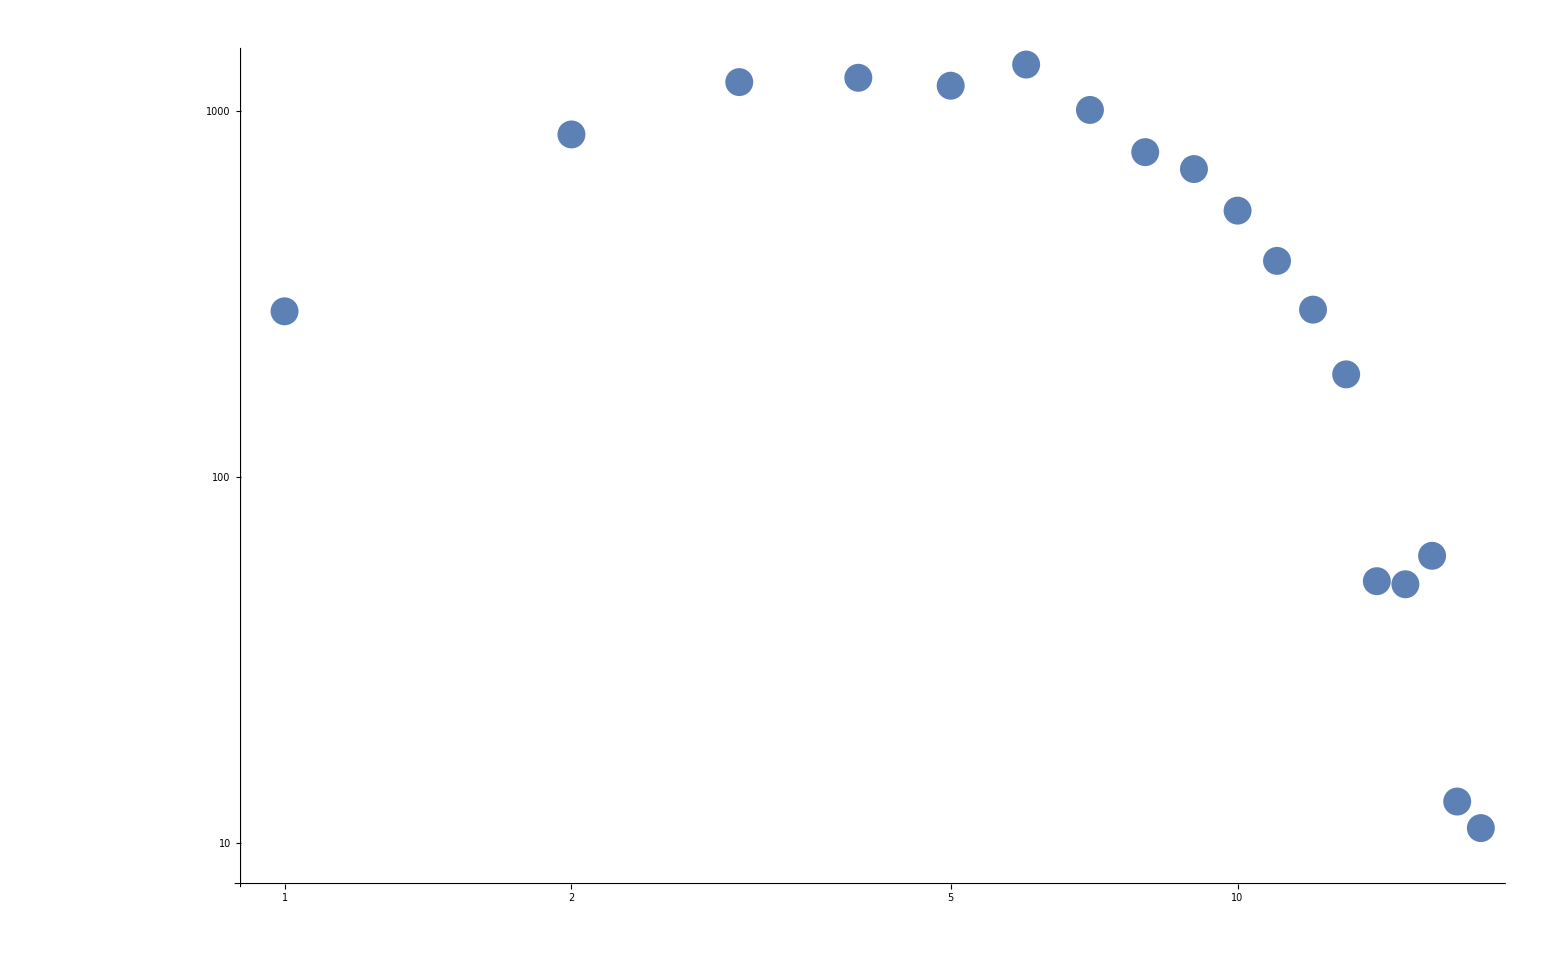

```mathematica
ListLogLogPlot[{chidata},PlotRange->All]
```

```mathematica
datanew=Import["array.txt", "CSV"]
```

{1}
 |  |  |  |

```mathematica
ArrayPlot[datanew, ColorFunction->"Rainbow"]
```

-Graphics-

```mathematica
chinewdata = Import["chinew.txt", "CSV"]
```

{{0,1},{1,3311},{2,1381},{3,699},{4,488},{5,345},{6,278},{7,211},{8,189},{9,161},{10,118},{11,126},{12,111},{13,84},{14,72},{15,77},{16,55},{17,57},{18,49},{19,42},{20,34},{21,48},{22,39},{23,38},{24,49},{25,35},{26,38},{27,28},{28,28},{29,32},{30,21},{31,22},{32,30},{33,27},{34,17},{35,17},{36,26},{37,17},{38,19},{39,18},{40,23},{41,21},{42,11},{43,15},{44,13},{45,14},{46,16},{47,11},{48,16},{49,15},{50,12},{51,14},{52,13},{53,13},{54,14},{55,10},{56,11},{57,11},{58,9},{59,10},{60,10},{61,10},{62,14},{63,13},{64,12},{65,12},{66,8},{67,6},{68,7},{69,9},{70,8},10025,{10096,0},{10097,0},{10098,0},{10099,0},{10100,0},{10101,0},{10102,0},{10103,0},{10104,0},{10105,0},{10106,0},{10107,0},{10108,0},{10109,0},{10110,0},{10111,0},{10112,0},{10113,0},{10114,0},{10115,0},{10116,0},{10117,0},{10118,0},{10119,0},{10120,0},{10121,0},{10122,0},{10123,0},{10124,0},{10125,0},{10126,0},{10127,0},{10128,0},{10129,0},{10130,0},{10131,0},{10132,0},{10133,0},{10134,0},{10135,0},{10136,0},{10137,0},{10138,0},{10139,0},{10140,0},{10141,0},{10142,0},{10143,0},{10144,0},{10145,0},{10146,0},{10147,0},{10148,0},{10149,0},{10150,0},{10151,1},{10152,0},{10153,0},{10154,0},{10155,0},{10156,0},{10157,0},{10158,0},{10159,0},{10160,0},{10161,0},{10162,0},{10163,0},{10164,0},{10165,0}}
 |  |  |  |

```mathematica
dataacc=chinewdata;
dataacc[[All,2]]=9729-Accumulate[(chinewdata[[All,2]])]
```

{9728,6417,5036,4337,3849,3504,3226,3015,2826,2665,2547,2421,2310,2226,2154,2077,2022,1965,1916,1874,1840,1792,1753,1715,1666,1631,1593,1565,1537,1505,1484,1462,1432,1405,1388,1371,1345,1328,1309,1291,1268,1247,1236,1221,1208,1194,1178,1167,1151,1136,1124,1110,1097,1084,1070,1060,1049,1038,1029,1019,1009,999,985,972,960,948,940,934,927,918,910,906,897,888,882,869,864,859,854,848,844,836,833,825,821,815,808,800,797,792,787,780,770,763,756,750,745,737,735,732,725,718,712,709,705,704,700,698,695,689,678,674,670,663,657,655,653,650,648,644,639,638,636,635,632,632,632,630,630,627,623,620,617,614,9898,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-314,-315,-315,-315,-315,-315,-315,-315,-315,-315,-315,-315,-315,-315,-315,-315}
 |  |  |  |

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

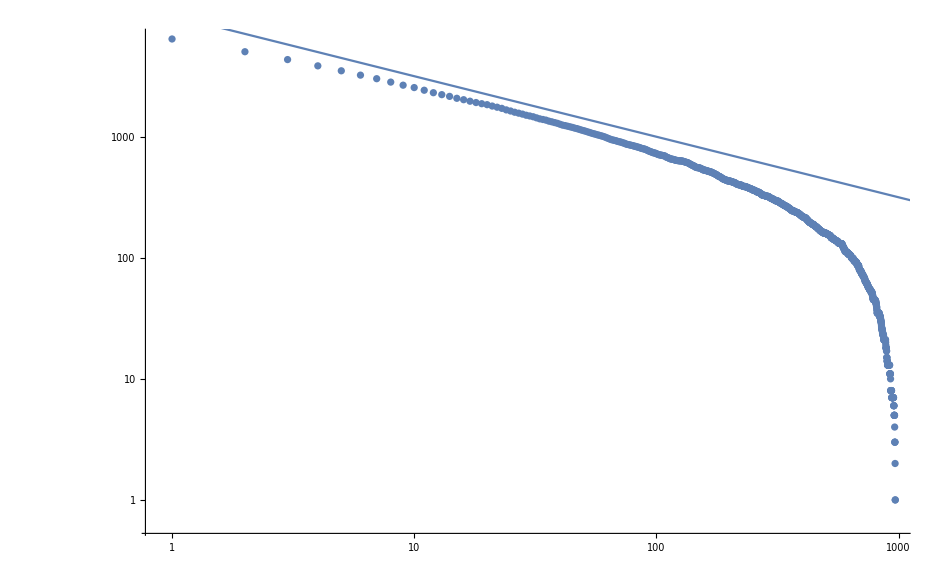

```mathematica
Show[ListLogLogPlot[{dataacc},PlotRange->All],LogLogPlot[10000/(x^0.5),{x,0.5,10000}]]
```

```mathematica
f = Import["fplot.txt" , "CSV"]
```

{{0,0},{3.87427×10^-7,2},{0.0456259,235533},{1.93714×10^-7,1},{0.0002311,1193},{0.0104987,54197},{1.93714×10^-7,1},{1.93714×10^-6,10},{3.87427×10^-7,2},{1.16228×10^-6,6},{2.9057×10^-6,15},{1.54971×10^-6,8},{1.93714×10^-7,1},{9.68568×10^-7,5},{1.93714×10^-7,1},{1.93714×10^-7,1},{9.68568×10^-7,5},{1.93714×10^-7,1},{1.93714×10^-7,1},{3.29313×10^-6,17},{0.00948906,48985},{2.32456×10^-6,12},{1.93714×10^-7,1},{0.0000482347,249},{1.93714×10^-7,1},{3.87427×10^-7,2},{3.87427×10^-7,2},{3.87427×10^-7,2},{0.0377646,194951},{0.0102513,52920},{3.09942×10^-6,16},{1.93714×10^-7,1},{1.93714×10^-7,1},{0.000157683,814},{3.87427×10^-7,2},{0.0102455,52890},{0.0455641,235214},10093,{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{5.81141×10^-7,3},{3.87427×10^-7,2},{1.93714×10^-7,1},{1.93714×10^-7,1},{5.81141×10^-7,3},{1.93714×10^-7,1},{1.93714×10^-7,1},{7.74854×10^-7,4},{1.93714×10^-7,1},{3.87427×10^-7,2},{5.81141×10^-7,3},{1.93714×10^-7,1},{5.81141×10^-7,3},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{3.87427×10^-7,2},{1.93714×10^-7,1},{1.93714×10^-7,1},{3.87427×10^-7,2},{1.93714×10^-7,1},{1.93714×10^-7,1},{5.81141×10^-7,3},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{3.87427×10^-7,2},{1.93714×10^-7,1}}
 |  |  |  |

```mathematica
fsort = f
```

{{0,0},{3.87427×10^-7,2},{0.0456259,235533},{1.93714×10^-7,1},{0.0002311,1193},{0.0104987,54197},{1.93714×10^-7,1},{1.93714×10^-6,10},{3.87427×10^-7,2},{1.16228×10^-6,6},{2.9057×10^-6,15},{1.54971×10^-6,8},{1.93714×10^-7,1},{9.68568×10^-7,5},{1.93714×10^-7,1},{1.93714×10^-7,1},{9.68568×10^-7,5},{1.93714×10^-7,1},{1.93714×10^-7,1},{3.29313×10^-6,17},{0.00948906,48985},{2.32456×10^-6,12},{1.93714×10^-7,1},{0.0000482347,249},{1.93714×10^-7,1},{3.87427×10^-7,2},{3.87427×10^-7,2},{3.87427×10^-7,2},{0.0377646,194951},{0.0102513,52920},{3.09942×10^-6,16},{1.93714×10^-7,1},{1.93714×10^-7,1},{0.000157683,814},{3.87427×10^-7,2},{0.0102455,52890},{0.0455641,235214},10093,{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{5.81141×10^-7,3},{3.87427×10^-7,2},{1.93714×10^-7,1},{1.93714×10^-7,1},{5.81141×10^-7,3},{1.93714×10^-7,1},{1.93714×10^-7,1},{7.74854×10^-7,4},{1.93714×10^-7,1},{3.87427×10^-7,2},{5.81141×10^-7,3},{1.93714×10^-7,1},{5.81141×10^-7,3},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{3.87427×10^-7,2},{1.93714×10^-7,1},{1.93714×10^-7,1},{3.87427×10^-7,2},{1.93714×10^-7,1},{1.93714×10^-7,1},{5.81141×10^-7,3},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{3.87427×10^-7,2},{1.93714×10^-7,1}}
 |  |  |  |

```mathematica
fsort[[1,All]]=SortBy[f,First]
```

{{0,0},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},10096,{0.00668564,34513},{0.00681252,35168},{0.00713234,36819},{0.00720711,37205},{0.00735705,37979},{0.00748451,38637},{0.00760945,39282},{0.00761623,39317},{0.00768423,39668},{0.00771135,39808},{0.00789596,40761},{0.00789712,40767},{0.0080486,41549},{0.00836552,43185},{0.00862219,44510},{0.00948906,48985},{0.00961323,49626},{0.0102455,52890},{0.0102513,52920},{0.0104987,54197},{0.0115054,59394},{0.0116625,60205},{0.0116755,60272},{0.0119605,61743},{0.0120436,62172},{0.0120852,62387},{0.0121896,62926},{0.0127039,65581},{0.0143032,73837},{0.0154256,79631},{0.0154661,79840},{0.0301044,155407},{0.0377646,194951},{0.0455641,235214},{0.0456259,235533}}
 |  |  |  |

```mathematica
facc=fsort;
facc[[1,All]]=Accumulate[(fsort[[1,All]])]
```

{{{0,0},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},{1.93714×10^-7,1},10097,{0.00681252,35168},{0.00713234,36819},{0.00720711,37205},{0.00735705,37979},{0.00748451,38637},{0.00760945,39282},{0.00761623,39317},{0.00768423,39668},{0.00771135,39808},{0.00789596,40761},{0.00789712,40767},{0.0080486,41549},{0.00836552,43185},{0.00862219,44510},{0.00948906,48985},{0.00961323,49626},{0.0102455,52890},{0.0102513,52920},{0.0104987,54197},{0.0115054,59394},{0.0116625,60205},{0.0116755,60272},{0.0119605,61743},{0.0120436,62172},{0.0120852,62387},{0.0121896,62926},{0.0127039,65581},{0.0143032,73837},{0.0154256,79631},{0.0154661,79840},{0.0301044,155407},{0.0377646,194951},{0.0455641,235214},{0.0456259,235533}},{1}}
 |  |  |  |

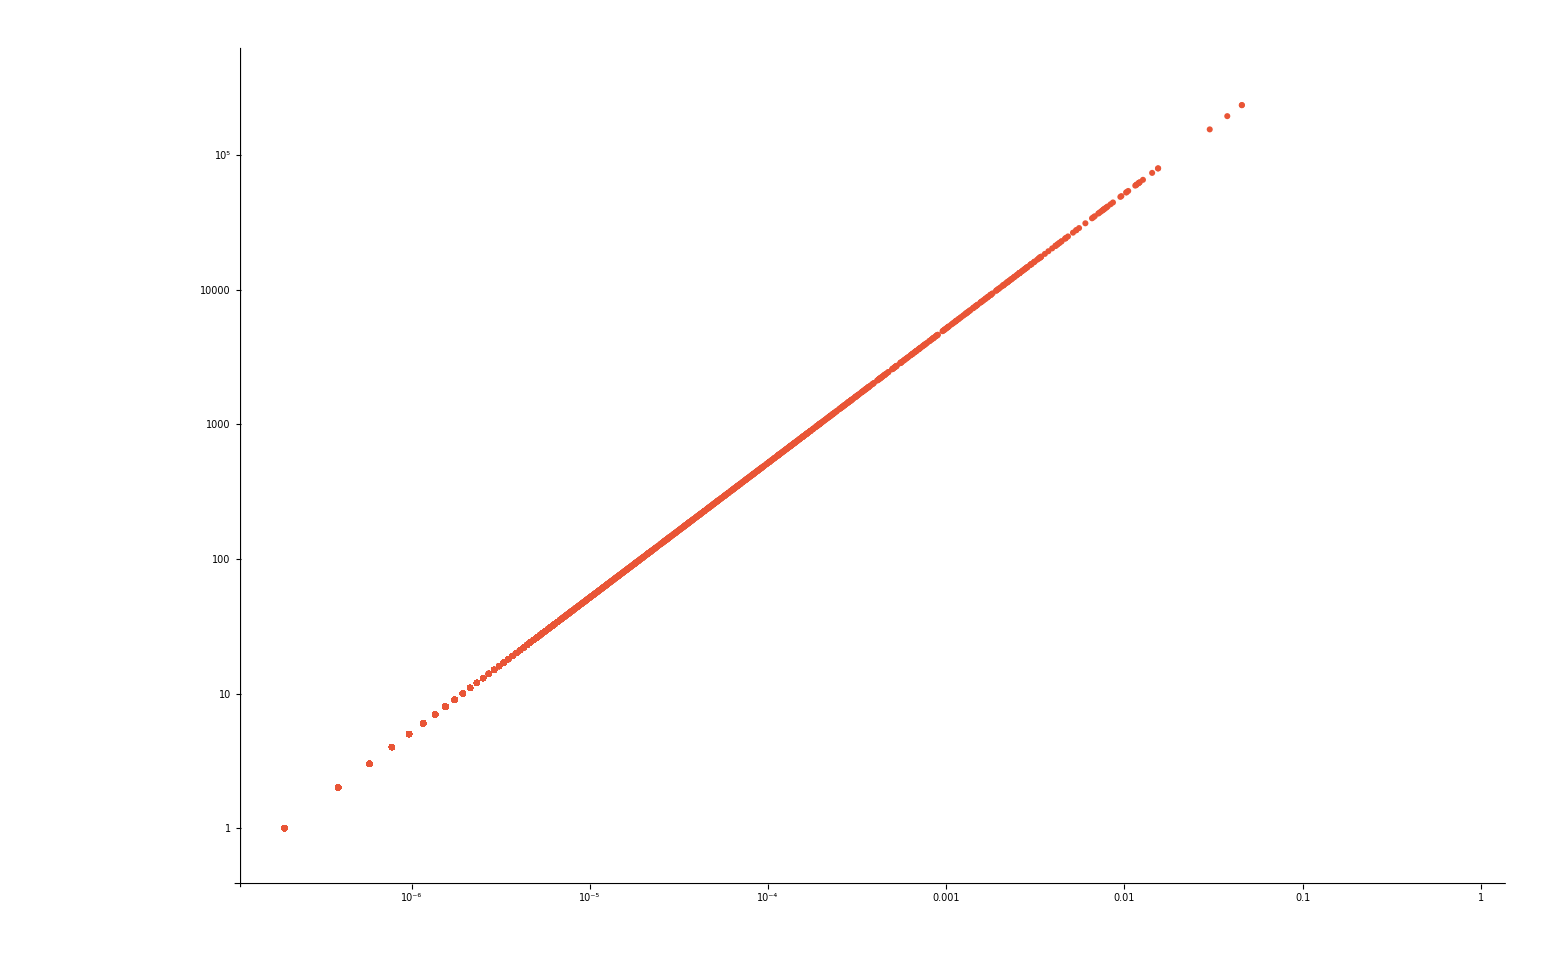

```mathematica
ListLogLogPlot[facc]
```